-1

1

2

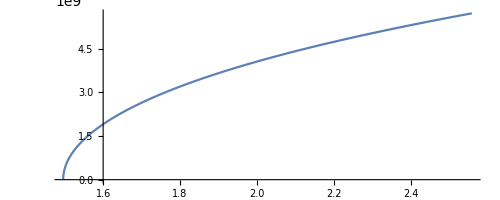

-1

```mathematica
(* 目标：转化为x关于t的微分方程+y关于t的微分方程 *)

(* 以下为常量 *)
RE := 1.496 * 10 ^ 11;
RM := 2.2794 * 10 ^ 11;
MS := 1.9891 * 10 ^ 30;
ME := 5.965 * 10 ^ 24;
MM := 6.4219 * 10 ^ 23; 
m := 2000;
TE := 3.1536 * 10 ^ 7;
TM := 5.93568 * 10 ^ 7;
OmegaE := 2 * Pi / TE; 
OmegaM := 2 * Pi / TM;
G := 6.672 59 * 10 ^ (-11);


(* 以下为初始条件 *)
ThetaE0 := 1; (* 地球初始角度 *)
ThetaM0 := 1; (* 火星初始角度 *)
X0X := RE; (* 初始x位置 *)
Y0Y := 0;(* 初始y位置 *)
V0X := 0; (* 初始x速度 *)
V0Y := 7900; (* 初始y速度 *)


(* 以下为末状态的时刻 *)
tend :=864000;


(* 以下为部分表达式 *)
cosTheta[t_] := x[t]/(√(x[t]^2+y[t]^2));
sinTheta[t_]:= y[t]/(√(x[t]^2+y[t]^2));

rS[t_] := Sqrt[ x[t]^2 + y[t]^2 ]; 

rE[t_] := Sqrt[  rS[t] ^ 2 + RE ^ 2 - 2 * rS[t] * RE * ( Cos[2*Pi-ThetaE0]*cosTheta[t] - Sin[2*Pi-ThetaE0]*sinTheta[t] )  ];
rM[t_] := Sqrt[  rS[t] ^ 2 + RM ^ 2 - 2 * rS[t] * RM * ( Cos[ ThetaM0 ]*cosTheta[t] + Sin[ThetaM0]*sinTheta[t] ) ];

ThetaE[t_] := Pi / 2 - (2*Pi - ThetaE0) - ArcCos[ (RE^2+rE[t]^2-rS[t]^2) / (2*RE*rE[t]) ] ;

ThetaM[t_] := ArcCos[ (RM^2 + rM[t]^2 - rS[t]^2)/(2*RM*rM[t]) ] - ThetaM0;

(* 以下是微分方程 *)
eqX := (   G*( MS/rS[t]^2 *cosTheta[t] +  ME/rE[t]^2*Cos[ThetaE[t] + Pi/2] + MM/rM[t]^2 * Cos[Pi-ThetaM[t]] ) - x''[t] == 0  );
eqY := (   G*( MS/rS[t]^2 *sinTheta[t] +  ME/rE[t]^2*Sin[ThetaE[t] + Pi/2] + MM/rM[t]^2 * Sin[Pi-ThetaM[t]] ) + y''[t] == 0  );

Print[1];
sol = NDSolve[  {eqX,eqY,x[0]== X0X,x'[0]== V0X, y[0] == Y0Y, y'[0]== V0Y } , {x,y} , {t,0,tend} ];
Print[2];
ParametricPlot[ Evaluate[ {x[t],y[t]}/.sol ] , {t,0,tend} , PlotRange->All ]

Print[Cos[Pi]];
```